```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
(*ICs - Initial Conditions *) (* Error while cosntraining u *)

CalculateSMatrix[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,τ_,A_]:= Module[{x,L,RHS,xdot,θ,θdot,u,K,S,soltn,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},

xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
Q = Grad[Grad[L,xState],xState]; (* Fix this *)
Mf = Grad[D[L,u],xState];
R = D[L,{u,2}];
S0 = ({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
RHS[t_] := (IdentityMatrix[4] + Afᵀ.S[t] + S[t].Af - KroneckerProduct[S[t].Bf,Bfᵀ.S[t]]) /. {x-> x1a[τ - t], xdot -> xdot1a[τ - t], θ ->θ1a[τ - t], θdot -> θdot1a[τ - t], u -> u1a[τ - t]};
sol2 = S /. NDSolve[{S'[t]== RHS[t],S[0]==S0},S,{t,0,τ }];
S = sol2[[1]]
]
CalculateGains[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,time_,A_,τ_,S_]:= Module[{x,L,RHS,xdot,θ,θdot,u,K,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
Bf = D[fx,u] ;(*For 1D stuff use D*)
K = (Bfᵀ.S[τ - time])/. {x-> x1a[time], xdot -> xdot1a[time], θ ->θ1a[time], θdot -> θdot1a[time], u -> u1a[time]};
K
]
ffCartPendulum[ICs_,n_,τ_,τ1_,A_,order_,maxIter_,maxError_,maxCount_,maxJ_,initGuess_]:=
Module[{InitGuess,J,S,K,count,error,x,dist,xdot,f,θ,θdot,λ1,λ2,λ3,λ4,Δt,bcs,eqns,sv,froot,xff,xdotff,xff0,xdotff0,θff0,θdotff0,uff0,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,i,xGuess = Table[Subscript[xGuess, i],{i,0,n}]},Δt=τ/n;
f[{x_,xdot_,θ_,θdot_,λ1_,λ2_,λ3_,λ4_}]:={
	xdot,
	1/(1-A Cos[θ]^2) (A θdot^2 Sin[θ]+1/(1-A Cos[θ]^2) (λ4 Cos[θ]-λ2)+A Cos[θ] Sin[θ]),
	θdot,
	1/(1-A Cos[θ]^2) (-(1/(1-A Cos[θ]^2))(-λ2 Cos[θ]+λ4 Cos[θ]^2)-Sin[θ]-A θdot^2 Cos[θ] Sin[θ]),
	0,
	-λ1,
	1/((-1+A Cos[θ]^2)^3)(A^2 (A θdot^2 λ2-λ4) Cos[θ]^5+A^3 (λ2-θdot^2 λ4) Cos[θ]^6-1/2 A^2 (λ2-θdot^2 λ4) Cos[θ]^4 (4-A+A Cos[2 θ])-A Cos[θ]^2 (-λ2+θdot^2 λ4+3 λ2 λ4 Sin[θ])+Cos[θ] (A θdot^2 λ2-λ4+(2 A λ2^2+λ4^2) Sin[θ]-2 A^2 θdot^2 λ2 Sin[θ]^2)+A Cos[θ]^3 (-2 A θdot^2 λ2+2 λ4+λ4^2 Sin[θ]+2 A (A θdot^2 λ2-λ4) Sin[θ]^2)+Sin[θ] (-λ2 λ4-A (λ2-θdot^2 λ4) Sin[θ]+A λ4 Sin[2 θ])),
	4 /(A Cos[2 θ]+A-2) (A θdot Sin[θ] (λ2-λ4 Cos[θ]))-λ3
};

InitGuess = initGuess;
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];

bcs={Subscript[x, 0]==ICs[[1]],Subscript[xdot, 0]==ICs[[2]],Subscript[x, n]==Subscript[xdot, n]==0,Subscript[θ, 0]==ICs[[3]],Subscript[θdot, 0]==ICs[[4]],Subscript[θdot, n]==0,Subscript[θ, n]==π};
eqns=Flatten[Join[bcs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}==
1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+
f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+
{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}],{i,1,n}]]];

sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1];

froot=FindRoot[eqns,sv,MaxIterations->maxIter];
error = Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]} - {0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]} - ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.froot,"Frobenius"];
uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
count = 0;
While[((error > maxError) || (J > maxJ)) && count <= maxCount ,
InitGuess = {RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}]};
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];
sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1];

froot=FindRoot[eqns,sv,MaxIterations->maxIter];
error = Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]} - {0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]} - ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.froot,"Frobenius"];
uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
count = count+1;
];


xff0=ListInterpolation[Table[Subscript[x, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
xdotff0=ListInterpolation[Table[Subscript[xdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ1ff0 = ListInterpolation[Table[Subscript[λ1, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ2ff0 = ListInterpolation[Table[Subscript[λ2, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ3ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ4ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
S = CalculateSMatrix[xff,xdotff,θff,θdotff,uff,τ,A];
K[t_] := CalculateGains[xff,xdotff,θff,θdotff,uff,t,A,τ,S];
{xff,xdotff,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,J,K}]

testSwingUp[ICs_,τ_,τ1_,uff0_,A_]:=Module[{eq,init,x,xdot,θ,θdot,xs,xdots,θs,θdots,t,J},
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (uff0[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (uff0[t]+A θdot[t]^2 Sin[θ[t]]))};
init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,uff0,J}]



testWithFB[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_,K_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J,error},
κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
ufb[t_] := Piecewise[{{K[t].{xff[t]-x[t],xdotff[t]-xdot[t],θff[t]-θ[t],θdotff[t]-θdot[t]},0<=t<=τ}},κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];
u[t_]:=uff[t]+ufb[t];

eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];us[t_]:=uff[t]+Piecewise[{{K[t].{xff[t]-xs[t],xdotff[t]-xdots[t],θff[t]-θs[t],θdotff[t]-θdots[t]},0<=t<=τ}},κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3(xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])];
J = NIntegrate[us[t]^2,{t,0,τ}];
error = Norm[{xs[τ],xdots[τ],θs[τ],θdots[τ]} - {0,0,Pi,0}];
{xs,xdots,θs,θdots,us,J,error}]

testWithFBClipped[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_,uBound_,K_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J,error},
κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
ufb[t_] := Piecewise[{{K[t].{xff[t]-x[t],xdotff[t]-xdot[t],θff[t]-θ[t],θdotff[t]-θdot[t]},0<=t<=τ}},κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];
u[t_]:= Clip[uff[t]+ufb[t],{-uBound,uBound}];

eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};

init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};

{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
us[t_]:=Clip[uff[t]+Piecewise[{{K[t].{xff[t]-xs[t],xdotff[t]-xdots[t],θff[t]-θs[t],θdotff[t]-θdots[t]},0<=t<=τ}},κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3(xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])],{-uBound,uBound}];
error = Norm[{xs[τ],xdots[τ],θs[τ],θdots[τ]} - {0,0,Pi,0}];

J = NIntegrate[us[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,us,J,error}]
```

```mathematica
ListBadICs = Import["BadICsFinal.mx"]
```

{{0.627505,1.5608,-1.87278},{1.1148,0.30864,1.12986},{-0.041697,-2.0371,-1.71718},{0.368226,-2.77245,-1.14628},{-1.0719,2.18965,-0.957474},{0.115931,-0.596853,-1.10108},{1.13482,0.250073,1.05297},{-0.539532,-1.31884,1.90383},{-0.751272,1.61411,-1.98849},{1.08726,1.27572,-1.33129},{-0.270006,2.63955,1.74043},{1.14973,-3.00487,1.14061},{0.538248,-2.80889,-1.80493},{1.58378,-0.32533,-0.270116},{-0.858177,-2.13384,-0.970321}}

```mathematica
Energy[{x1_,x2_,θ1_,θ2_,A_}] := 1/2*x2^2 + 1/2*A*θ2^2 + A*Cos[θ1]*x2*θ2 - A*Cos[θ1];
```

0.379218

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$565051 near {t$565051} = {2.80263}. NIntegrate obtained 29.4665 and 0.0000394829 for the integral and error estimates.

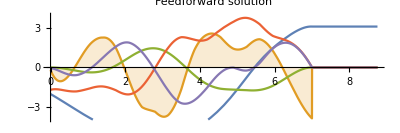
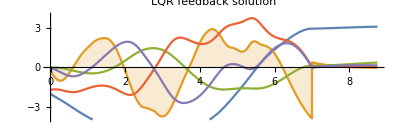
-Graphics- | -Graphics-

0.216654

```mathematica
n=20;τ=7;τ1=τ*1.25;A=0.2;order = 4;maxIter = 100;maxError = 0.01;uMax = 5;maxCount = 5;
xdotMin = -2;
xdotMax = 2;
θMin = -π;
θMax = π;
θdotMin = -2;
θdotMax = 2;

xdotInit = RandomReal[{xdotMin,xdotMax}];
θInit = RandomReal[{θMin,θMax}];
θdotInit = RandomReal[{θdotMin,θdotMax}];
ICs = {0,xdotInit,θInit,θdotInit};
ICs = {0,-0.041696955118863066,-2.037097470033123,-1.7171764604240014};
maxJ = 2^2*τ;
InitGuess = {0,0,0,0};
EInitial = Energy[Join[Table[ICs[[i]],{i,1,4}],{A}]]
{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,Jff,K}=Quiet[ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter,maxError,maxCount,maxJ,InitGuess]]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J,error}=testWithFBClipped[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A,uMax,K];
p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"LQR feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
Grid[{{p1a,p1c}}]
error
```

```mathematica
J
```

11.1266

```mathematica
ListBadICs
```

{{-1.59192,-2.62656,-1.83377},{0.898842,-2.78157,-1.72083},{1.513,-2.76388,-1.54996},{-1.12588,-3.07566,-1.81809},{1.08622,1.38908,1.24186},{1.41081,-2.67997,-1.2495},{1.80182,0.63122,0.300731},{1.66393,0.376293,0.929048},{-0.0370686,1.26221,0.846679},{-0.543465,-2.60184,-1.76565},{1.27717,-2.93965,-1.4976},{1.59188,-2.89868,-0.804337},{1.88814,-2.33942,-1.83701},{1.07447,-1.72856,-1.9549},{0.949879,1.4435,1.02116},{-0.909698,-1.61604,-1.95239},{0.401394,-2.48837,-1.34319}}

```mathematica
Etable = Table[Energy[Join[Table[Join[{0},ListBadICs[[j]]][[i]],{i,1,4}],{A}]],{j,1,Dimensions[ListBadICs][[1]]}]
```

{1.26933,1.17678,2.00668,0.755412,0.756766,1.64605,1.55835,1.57218,0.00972404,0.466365,1.61056,1.77443,2.74126,1.05683,0.55465,0.787939,0.50543}

```mathematica
ListBadICs[[17]]
```

{0.401394,-2.48837,-1.34319}

```mathematica
(* Monte Carlo Simulation Script*)
nGrid = 5;

xdotMin = -2;
xdotMax = 2;
θMin = -π;
θMax = π;
θdotMin = -2;
θdotMax = 2;
n=20;τ=5;τ1=τ*1.25;A=0.2;order = 4;maxIter = 30;maxError = 0.01;uMax = 2;maxCount = 10;
maxJ = uMax^2*τ;
m = Table[Table[Table[
xIC = 0;
xdotIC = xdotMin + i*(xdotMax - xdotMin)/nGrid;
θIC = θMin + j*(θMax - θMin)/nGrid;
θdotIC = θdotMin + k*(θdotMax - θdotMin)/nGrid;
ICs = {xIC,xdotIC,θIC,θdotIC};

InitGuess = {0,0,0,0};
{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,Jff,K}=Quiet[ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter,maxError,uMax,maxCount,maxJ,InitGuess]]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J,error}=Quiet[testWithFBClipped[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A,uMax,K]];
error,{i,0,nGrid}],{j,0,nGrid}],{k,0,nGrid}];
x = Table[Table[Table[If[m[[i]][[j]][[k]] < 1,{xdotMin + i*(xdotMax - xdotMin)/nGrid,θMin + j*(θMax - θMin)/nGrid,θdotMin + k*(θdotMax - θdotMin)/nGrid},##&[]],{i,1,nGrid}],{j,1,nGrid}],{k,1,nGrid}];
x = Flatten[x,1];
x = Flatten[x,1];
ListPointPlot3D[x,AxesLabel->{"xdot","θ"},PlotLabel->"θdot"]
Export["myFile.mx",x]
```

```mathematica
(* Monte Carlo Simulation Script*)
nGrid = 50;

xdotMin = -2;
xdotMax = 2;
θMin = -π;
θMax = π;
θdotMin = -2;
θdotMax = 2;
n=20;τ=5;τ1=τ*1.25;A=0.2;order = 4;maxIter = 30;maxError = 0.01;uMax = 2;maxCount = 10;
maxJ = uMax^2*τ;
m = Table[Table[Table[
xIC = 0;
xdotIC = xdotMin + i*(xdotMax - xdotMin)/nGrid;
θIC = θMin + j*(θMax - θMin)/nGrid;
θdotIC = θdotMin + k*(θdotMax - θdotMin)/nGrid;
ICs = {xIC,xdotIC,θIC,θdotIC};

InitGuess = {0,0,0,0};
{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,Jff,K}=Quiet[ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter,maxError,uMax,maxCount,maxJ,InitGuess]]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J,error}=Quiet[testWithFBClipped[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A,uMax,K]];
error,{i,0,nGrid}],{j,0,nGrid}],{k,0,nGrid}];
```

```mathematica
x = Table[Table[Table[If[m[[i]][[j]][[k]] < 1,{xdotMin + i*(xdotMax - xdotMin)/nGrid,θMin + j*(θMax - θMin)/nGrid,θdotMin + k*(θdotMax - θdotMin)/nGrid},##&[]],{i,1,nGrid}],{j,1,nGrid}],{k,1,nGrid}];
x = Flatten[x,1];
x = Flatten[x,1];
ListPointPlot3D[x,AxesLabel->{"xdot","θ"},PlotLabel->"θdot"]
```

```mathematica
Export["myFile.mx",x]
```

```mathematica
Import["myFile.mx"]
```

### Work with Random Initial Conditions

```mathematica
iter = 0;
iterMax = 500;
Results = {};
BadICs = {};
correctCount = 0;
While[iter <= iterMax,
n=20;τ=7;τ1=τ*1.25;A=0.2;order = 4;maxIter = 100;maxError = 0.01;uMax = 2;maxCount = 20;
xdotMin = -2;
xdotMax = 2;
θMin = -π;
θMax = π;
θdotMin = -2;
θdotMax = 2;

xdotInit = RandomReal[{xdotMin,xdotMax}];
θInit = RandomReal[{θMin,θMax}];
θdotInit = RandomReal[{θdotMin,θdotMax}];
ICs = {0,xdotInit,θInit,θdotInit};
Print[ICs];
maxJ = uMax^2*τ;
InitGuess = {0,0,0,0};{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,Jff,K}=Quiet[ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter,maxError,uMax,maxCount,maxJ,InitGuess]]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J,error}=Quiet[testWithFBClipped[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A,uMax,K]];
If[error < 1, Print["Works"];Results = Append[Results,Table[ICs[[i]],{i,2,4}]];correctCount = correctCount+1,
BadICs = Append[BadICs,Table[ICs[[i]],{i,2,4}]];Print["Failed"]];
iter = iter + 1;
];
Print[correctCount];
ListPointPlot3D[Results,AxesLabel->{"xdot","θ"},PlotLabel->"θdot"]
ListPointPlot3D[BadICs,AxesLabel->{"xdot","θ"},PlotLabel->"θdot"]
Export["Results.mx",Results]
Export["BadICs.mx",BadICs]
```

-Graphics3D-

-Graphics3D-

Results.mx

BadICs.mx

```mathematica
ListBadICs = Import["BadICs.mx"];
```

```mathematica
ListPointPlot3D[Results,AxesLabel->{"xdot","θ"},PlotLabel->"θdot"]
ListPointPlot3D[BadICs,AxesLabel->{"xdot","θ"},PlotLabel->"θdot"]
```

-Graphics3D-

-Graphics3D-

### Run the Bad ICs with Tau = 5

```mathematica
iter = 1;
iterMax = Dimensions[ListBadICs][[1]]
Results = {};
BadICs = {};
correctCount = 0;
While[iter <= iterMax,
n=20;τ=5;τ1=τ*1.25;A=0.2;order = 4;maxIter = 100;maxError = 0.01;uMax = 2;maxCount = 20;
ICs = Join[{0},ListBadICs[[iter]]];
Print[ICs];
maxJ = uMax^2*τ;
InitGuess = {0,0,0,0};{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,Jff,K}=Quiet[ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter,maxError,maxCount,maxJ,InitGuess]]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J,error}=Quiet[testWithFBClipped[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A,uMax,K]];
If[error < 1, Print["Works"];Results = Append[Results,Table[ICs[[i]],{i,2,4}]];correctCount = correctCount+1,
BadICs = Append[BadICs,Table[ICs[[i]],{i,2,4}]];Print["Failed"]];
iter = iter + 1;
];
Print[correctCount];
ListPointPlot3D[Results,AxesLabel->{"xdot","θ"},PlotLabel->"θdot"]
ListPointPlot3D[BadICs,AxesLabel->{"xdot","θ"},PlotLabel->"θdot"]
```

-Graphics3D-

-Graphics3D-

```mathematica
Export["BadICs.mx",BadICs]
```

BadICs.mx

```mathematica
Dimensions[BadICs]
```

{17,3}

```mathematica
ICs = {0,0,0,0};
Energy[Join[Table[ICs[[i]],{i,1,4}],{A}]]
```

-0.2

### Run Final Simulations with E < 1, n = 40, Tau = 7

```mathematica
iter = 1;
iterMax = 300;
Results = {};
BadICs = {};
correctCount = 0;
While[iter <= iterMax,
n=40;τ=7;τ1=τ*1.25;A=0.2;order = 4;maxIter = 100;maxError = 0.01;uMax = 5;maxCount = 5;
xdotMin = -2;
xdotMax = 2;
θMin = -π;
θMax = π;
θdotMin = -2;
θdotMax = 2;

xdotInit = RandomReal[{xdotMin,xdotMax}];
θInit = RandomReal[{θMin,θMax}];
θdotInit = RandomReal[{θdotMin,θdotMax}];
ICs = {0,xdotInit,θInit,θdotInit};

If[Energy[Join[Table[ICs[[i]],{i,1,4}],{A}]] < 1,
Print[ICs];
maxJ = 2^2*τ;
InitGuess = {0,0,0,0};{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,Jff,K}=Quiet[ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter,maxError,maxCount,maxJ,InitGuess]]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J,error}=Quiet[testWithFBClipped[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A,uMax,K]];
If[error < 1, Print["Works"];Results = Append[Results,Table[ICs[[i]],{i,2,4}]];correctCount = correctCount+1,BadICs = Append[BadICs,Table[ICs[[i]],{i,2,4}]];Print["Failed"]];
iter = iter + 1;
,
_
];

];
Print[correctCount];
ListPointPlot3D[Results,AxesLabel->{"xdot","θ"},PlotLabel->"θdot"]
ListPointPlot3D[BadICs,AxesLabel->{"xdot","θ"},PlotLabel->"θdot"]
Export["ResultsFinal.mx",Results]
Export["BadICsFinal.mx",BadICs]
```

{0,1.03814,-0.0523347,-1.36527}

Works

{0,-1.05253,1.04795,1.54303}

Works

{0,0.933152,0.861195,-1.91934}

Works

{0,-0.98234,-2.15054,-0.938723}

Works

{0,0.271017,-2.78512,1.48164}

Works

{0,-0.341249,1.80635,0.779739}

Works

{0,-0.721151,-0.651771,1.54923}

Works

{0,-1.14514,-1.85228,-0.062643}

Works

{0,-0.775234,-2.022,1.96851}

Works

{0,1.38575,-2.78698,1.49962}

Works

{0,1.56826,-0.131744,-1.98877}

Works

{0,-0.559074,-3.01859,0.0712061}

Works

{0,-0.0554339,0.432278,-0.0778896}

Works

{0,0.0887175,0.568103,0.944731}

Works

{0,0.369834,1.17331,-1.76255}

Works

{0,1.01094,2.3406,-0.0456038}

Works

{0,-0.0774261,-1.63876,1.9238}

Works

{0,-0.138609,-2.943,0.0591095}

Works

{0,0.392451,2.31446,1.4889}

Works

{0,1.00466,-0.542166,-1.84253}

Works

{0,0.627505,1.5608,-1.87278}

Failed

{0,1.1148,0.30864,1.12986}

Failed

{0,0.755452,-0.560026,-1.75106}

Works

{0,-1.03704,1.26928,1.64273}

Works

{0,1.00823,0.126203,-0.21533}

Works

{0,-0.041697,-2.0371,-1.71718}

Failed

{0,-1.13,1.75077,-1.84726}

Works

{0,0.368226,-2.77245,-1.14628}

Failed

{0,0.524924,0.922164,1.81771}

Works

{0,0.4441,1.78385,-1.85346}

Works

{0,0.36134,2.1208,1.91498}

Works

{0,0.324187,0.862081,-0.413214}

Works

{0,0.680556,-1.71772,-0.0221645}

Works

{0,-0.706788,-0.640621,-1.15565}

Works

{0,0.999296,0.686786,1.82139}

Works

{0,-1.14167,-0.390459,0.579333}

Works

{0,-0.168906,1.48835,-1.60069}

Works

{0,-1.0719,2.18965,-0.957474}

Failed

{0,0.889508,-1.24649,0.101004}

Works

{0,-1.46207,-0.577624,-0.244726}

Works

{0,0.115931,-0.596853,-1.10108}

Failed

{0,-0.395675,-1.41989,-0.625085}

Works

{0,0.643104,-0.857315,-0.651652}

Works

{0,0.471547,-0.56939,1.65881}

Works

{0,0.585655,1.83772,1.30777}

Works

{0,0.0805998,2.72837,-0.0953968}

Works

{0,0.899784,1.63162,-1.53379}

Works

{0,0.933475,-1.09034,-0.949981}

Works

{0,-1.08357,-2.09321,0.733459}

Works

{0,-0.316946,3.12667,-1.36394}

Works

{0,0.401476,2.77279,-0.252172}

Works

{0,1.13482,0.250073,1.05297}

Failed

{0,-1.12004,0.73537,0.637024}

Works

{0,0.331053,1.43412,1.38397}

Works

{0,-0.539532,-1.31884,1.90383}

Failed

{0,-1.06078,2.42947,-0.0458715}

Works

{0,0.0308427,-1.08893,-0.336889}

Works

{0,-0.466502,-0.484957,-1.16897}

Works

{0,-0.173909,0.784146,0.353411}

Works

{0,-0.747162,1.49392,1.56077}

Works

{0,0.228365,0.361582,-1.11678}

Works

{0,0.873182,-2.58381,-0.188312}

Works

{0,-1.3204,-0.107833,0.623148}

Works

{0,-0.076111,-2.07339,-0.884175}

Works

{0,-0.80777,0.614304,0.503978}

Works

{0,1.31364,-1.06245,-1.06774}

Works

{0,-0.751272,1.61411,-1.98849}

Failed

{0,-0.640533,2.70337,0.445024}

Works

{0,0.847261,-2.89874,0.290872}

Works

{0,-1.22127,-2.59264,-0.345339}

Works

{0,0.487515,-1.53974,-0.0849625}

Works

{0,1.01062,2.95671,0.333337}

Works

{0,0.0626654,0.760047,1.89881}

Works

{0,-0.830957,-1.0083,1.64406}

Works

{0,1.08726,1.27572,-1.33129}

Failed

{0,0.946383,0.471554,-0.517801}

Works

{0,1.0902,2.13939,-0.146787}

Works

{0,-0.270006,2.63955,1.74043}

Failed

{0,1.05931,0.36354,-1.45555}

Works

{0,1.32971,0.505847,-0.96664}

Works

{0,1.07289,-0.907843,-1.59852}

Works

{0,-0.766458,2.26112,-0.730997}

Works

{0,0.471544,0.757932,-0.157109}

Works

{0,-0.33541,1.48395,1.02644}

Works

{0,1.34441,2.82728,0.756856}

Works

{0,-0.223273,-0.640764,1.95138}

Works

{0,-1.23983,0.296398,1.11814}

Works

{0,1.14973,-3.00487,1.14061}

Failed

{0,-0.952595,2.69224,-0.445392}

Works

{0,0.024925,-3.07226,1.74211}

Works

{0,0.81662,1.54257,-0.347324}

Works

{0,-0.202954,1.76429,1.61982}

Works

{0,-0.87499,-1.99799,0.34921}

Works

{0,-0.201372,-1.99501,1.71491}

Works

{0,0.170386,2.70646,0.1162}

Works

{0,1.21411,0.737369,-0.29156}

Works

{0,0.339751,-1.33701,-0.934008}

Works

{0,0.675499,-0.183817,-1.59383}

Works

{0,-0.506907,0.94298,-0.662502}

Works

{0,-1.04779,0.478673,0.900589}

Works

{0,-0.755686,-0.347161,-1.89419}

Works

{0,-0.947523,1.01286,0.0443177}

Works

{0,0.433424,2.96865,0.601247}

Works

{0,0.538248,-2.80889,-1.80493}

Failed

{0,1.28258,-1.14381,-1.80286}

Works

{0,0.723095,-0.41504,1.63714}

Works

{0,0.195392,-1.55814,0.756818}

Works

{0,-0.563041,-1.27646,1.47526}

Works

{0,-1.16676,-0.389174,1.58839}

Works

{0,0.992995,-1.39482,1.72015}

Works

{0,-0.701414,-1.60343,-1.07249}

Works

{0,-0.704449,-0.845474,1.86246}

Works

{0,-0.361728,-0.360232,0.970822}

Works

{0,-1.14666,1.84996,-0.78329}

Works

{0,-0.201116,2.38945,0.0275587}

Works

{0,1.58378,-0.32533,-0.270116}

Failed

{0,1.42123,0.203677,0.099937}

Works

{0,1.06866,0.259118,-0.218457}

Works

{0,0.199566,-2.67218,1.0109}

Works

{0,0.412958,-2.4277,1.95015}

Works

{0,-0.773588,-2.18862,-0.452153}

Works

{0,0.720552,-1.62414,0.651564}

Works

{0,1.0323,1.39368,0.276376}

Works

{0,1.09326,0.659295,1.44295}

Works

{0,0.766034,-0.0709903,-1.61974}

Works

{0,1.21013,-2.39494,0.273166}

Works

{0,-0.564565,-1.73727,-0.51259}

Works

{0,0.797724,1.12886,-1.6525}

Works

{0,-0.409567,1.77006,-1.80007}

Works

{0,-0.0927313,-0.246616,0.0426791}

Works

{0,0.833839,2.23843,-0.244557}

Works

{0,0.305726,-2.45938,1.96892}

Works

{0,-0.372452,-0.827925,1.31807}

Works

{0,-1.05318,-2.06438,-1.32784}

Works

{0,0.701707,-1.078,0.39933}

Works

{0,-0.241499,0.543118,-0.107474}

Works

{0,-0.0249538,0.213504,-1.23339}

Works

{0,1.0479,2.12738,-0.275014}

Works

{0,-0.858177,-2.13384,-0.970321}

Failed

{0,0.230803,2.78593,1.06342}

Works

{0,-0.751179,-2.55959,0.130604}

Works

{0,-0.966076,-0.864211,-1.71186}

Works

{0,1.00257,-0.202009,-1.27765}

Works

{0,-0.938219,0.132411,0.194793}

Works

{0,-1.33678,-1.51323,-0.769265}

Works

{0,0.0821146,1.30806,1.30763}

Works

{0,-0.402384,-2.32053,-1.78052}

Works

{0,0.582675,-2.57877,0.422176}

Works

{0,-0.0979499,-2.38442,-0.119004}

Works

{0,-1.13874,0.547386,-0.955117}

Works

{0,-0.652791,0.893333,1.0348}

Works

{0,-0.166428,-3.06106,0.327388}

Works

{0,-0.633436,1.15646,1.52326}

$Aborted

137

-Graphics3D-

-Graphics3D-

ResultsFinal.mx

BadICsFinal.mx

```mathematica
correctCount
```

137